```mathematica
Quit
```

## Data **

```mathematica
SetDirectory[NotebookDirectory[]];
Get["g20"];
```

```mathematica
mutilde=10;
bSub=10^-5;
```

```mathematica
background=newton[initguess[1/mutilde],abc/.{b0->bSub,temp->1/mutilde},abc2/.{b0->bSub,temp->1/mutilde}]
```

start norm: 8.180×10^-4

iteration: 1 norm: 1.390×10^-9		 T subt: 1.248  T solve: 0.1404

iteration: 2 norm: 0.×10^-20		 T subt: 1.186  T solve: 0.0624001

overall time: 2.88601

{-1.94312266155280005253413814276465099908333858910630029842266,-1.94307880303752749211277839080204008988576098988028662774093,-1.94243046344296793426487091796488074424233230360533393233942,-1.93969757564479245537145872720956334204812430633231880821818,-1.93263944650020246127573828922814034761521642757394988313418,-1.918566769207539544638708871180739419193429535717883977362,-1.89472727203344453289094103460326237012757901062939146925239,-1.85872064229149752036094132067643383605779653417718188289417,-1.80889457959582818269592799744145879583741753758495427272058,-1.74467535172734924438746534308699836574547111018282880691502,-1.66679289963536313349879057121586522008597714889420282764425,-1.5773716535886980803099788791481203106914825826856367073202,-1.47987258425589957466661968603237418112364387930403747735536,-1.37888806940996843774962589138982930024102629002065732966211,-1.27980717075183997696872539598066051917715729962802072908975,-1.18838314893651322687028360697460154598911493132025212930404,-1.11024595063940763775486803136922532187973978596509339035903,-1.05040878910691443982611233617881945340810142665479840872669,-1.01281910531944698134066174696045831432765490847489757089175,-1.,3.9950483316590553043888412128033996750401339887272496372019×10^-12,3.9944635028802931624471446178224069797725632165942894057142×10^-12,3.985809828535092298952022602190448095628603944196301013395×10^-12,3.9492414965065872035839448806141156817785134269394123519796×10^-12,3.8545218596202233863483419516256971127597737701209511873233×10^-12,3.6657630088101348529171260259088150420147606869035033811441×10^-12,3.3490584770538429433208910053970474403471882106583007272465×10^-12,2.882308132294961055846525965577079276679566966546261760016×10^-12,2.2640264770310978313099694491643319749320657915277414218361×10^-12,1.5169119490187352387967406470273183957236356167648817521373×10^-12,6.8418263762316122478736827281223962050502421745275139185216×10^-13,-1.794821668523707335310016240632535358407186488828748185831×10^-13,-1.0184176402386262891752667326777064220129714175257288773326×10^-12,-1.784556551972934651369399684098692326727236138652930243132×10^-12,-2.4427503801167371142629253408014872700961562863733346365123×10^-12,-2.9729048904386974983216908892029253441792526874689766298717×10^-12,-3.3694273767875333617185381988268756201242427515307221548478×10^-12,-3.6382639645793417587240745676716600586332719834572039859729×10^-12,-3.791636202214155084131946110467480845104084113122583376024×10^-12,-3.8411767300167405415193160316825262242566673099703429276257×10^-12,-1.9975241658045985458705967265505286628780793722104246826685×10^-12,-1.997377939213206745499295897979273181486235247064756368343×10^-12,-1.9952104283302764763452874572648090333491397481723620401998×10^-12,-1.9859934507939204751912452918041528874981918653661544688144×10^-12,-1.9617937454524890058671867940018922507653460520080374948071×10^-12,-1.9125132539710330985927543659211063247392307266011569997023×10^-12,-1.8274400675902240950521791506152987859152411442379901657463×10^-12,-1.6978642883701729278528720898252003921161471418065772947371×10^-12,-1.5201259017225218074959338785434327281884083391739910835629×10^-12,-1.2977042398954782085868446497612270335520662224267498124297×10^-12,-1.0412262552534944104510949975070938118609430905236232082817×10^-12,-7.664271840686140090610333177664601860910008070605301316833×10^-13,-4.9107990850130126993696760373503878547490555670065180334465×10^-13,-2.320365836795559452801415250307386500378169925708203853117×10^-13,-3.04627608994782573362856063627950070829417486395420019949×10^-15,1.864902467137723575118399792453288897544487549082005734943×10^-13,3.3188521538168780604889265499948149643002577059692996857749×10^-13,4.3266371029011319937035889531210128262713401195815477014543×10^-13,4.9113717540779901090790102479926825317219808138672306636551×10^-13,5.102011133445241893914786444762554007122603040597024449521×10^-13,4.08384091892633592200185672912199732212540660543875547148611×10^-6,4.11162631802270876112815931811212062769732278067785379617774×10^-6,4.1934520089900122280520311422920585187108438753156203097881×10^-6,4.32471380878834012892714748245156248828437996849699881337496×10^-6,4.49776469114310030834160383573257480779576388233824512649131×10^-6,4.70216636300370440810363376391561766040288917135640470576386×10^-6,4.925353810832427802199668313625978478963895118211930102355×10^-6,5.15377587340253599112099825154615101060174515348325952343438×10^-6,5.37433531521940447130103098899618855480245224398873904077347×10^-6,5.57575846086406187071027333465729314158035133838437882557261×10^-6,5.74954442927049419328366822573509517703099547664373399369332×10^-6,5.89037034775418652350348021808655335440670705947667531040528×10^-6,5.99607482238737544238745761620217728079774493813638444069169×10^-6,6.06743951339491566478709556479845431990618355671797408019101×10^-6,6.10792387902667168469171035575492654591269620369054075922899×10^-6,6.1233647424037260722483600715093020101844706772087854438036×10^-6,6.12150855866077136020061011016484954181265023630837145734793×10^-6,6.11115594589517796134165596573899705344444639520814731785494×10^-6,6.1007471926640313873304013034029891110379381806778234715627×10^-6,6.09650758755706255713225017558426079554036954995218470496713×10^-6,1.68207252656906792316475261873187927851710365360651823884986,1.69354316499131291818985219009763765311356838941658609464886,1.72764219114360122905040766763273802646148104481729240058741,1.78343947248199315214451173586543015721762654759510778589795,1.85941300462417876969131194266291174502211865132678073777786,1.95349042766145863970699258317873133530602726615416621488281,2.06310555473481902341924227365468014848231259312226586013668,2.18526837092290595120412550282771264338403134914660048837207,2.31664659305470504474162999904378950761246070649195548588641,2.45365656570784324064173975756394913290485774056815518815034,2.59256101398662447431454732558937857106930399538150237638893,2.72957098663883935302353470441444545662554686414489439861657,2.86094920876887319385401501646208444334010663334979872579956,2.9831120249545210296922996545161240265062972577188992466399,3.09272715202502278663425490617807815390962400261142325839216,3.18680457505934495000073246635445404834329534266613360950014,3.26277810719881625318700365717302160281229200134009521073934,3.31857538853504512459744922342374999511467695540652551248403,3.35267441468594913729059262902790611423159931387020403650767,3.36414505310771902921344054192784761417616057452836710539242,-9.71145026012089092983967490726585782125984581490663269556727×10^-6,-9.71122446050555622105711615106237157828245225351500905892731×10^-6,-9.70788858853975573159619745300777397039254729322206484317317×10^-6,-9.69386853008579573172166037613350282568976011484480003028556×10^-6,-9.65796465158452327763423315865674554118089381513581385197277×10^-6,-9.58765398248750319327041663003452397906363827861694073006698×10^-6,-9.47221750201071514875099406803940204872286489275802988045464×10^-6,-9.30589215597529602973301607696567743300834371555657938527584×10^-6,-9.08980984127615104569074345870582411652667908185724816401003×10^-6,-8.83183425804791425115073839810332090490318757162229758885081×10^-6,-8.54449946026403665059789558609695538378524265422846844494999×10^-6,-8.24221439735328077829928415021501641648862626290938930598951×10^-6,-7.93897576154562081191853856260701811158649275819150694296898×10^-6,-7.64719531224993592199673660100690327824765542812698048368403×10^-6,-7.3775619956877047022096348273952528581556408235576080961854×10^-6,-7.13950774475980980938178493743722744922781176942204904188706×10^-6,-6.94178150196888213747393866420066966888508234299946918502966×10^-6,-6.79268187729194433133277076081915625441074544102874654622406×10^-6,-6.69961143515051094134080508087266745077471463823027772392676×10^-6,-6.66792629594914964769155762739915087732644129077052306083988×10^-6}

```mathematica
γSub=2/(√3);
μSub=mutilde;
bSub=bSub;
```

```mathematica
prec1=60;
gSize=1/6 Length[background];
zgrid=SetPrecision[Table[1/2 (1-Cos[(n π)/(gSize-1)]),{n,0,gSize-1}],prec1];
{uSub,wSub,vSub,cSub,avSub,pSub}=Interpolation[{zgrid,background⟦gSize #+1;;gSize(#+1)⟧}//Transpose]&/@Range[0,5];

backSub=SetPrecision[{u->uSub,w->wSub,vv->vSub,c->cSub,AV->avSub, P->pSub},prec1];
```

## Loading things

### Matrix

```mathematica
firstTotal=({{-(u[z] w[z])/(2 z), 0, 0, 0, 0, 0, 0, 0}, {0, -(u[z] w[z])/(2 z), 0, 0, 0, 0, 0, 0}, {0, 0, w[z]/(2 z^3), 0, -(c[z] w[z])/(2 z^3), 0, 0, 0}, {0, 0, 0, w[z]/(2 z^3), 0, -(c[z] w[z])/(2 z^3), 0, 0}, {0, 0, -(c[z] w[z])/(2 z^3), 0, (u[z]-c[z]^2 w[z]^2)/(2 z^3 w[z])+(-u[z]+c[z]^2 w[z]^2)/(z^3 w[z]), 0, 0, 0}, {0, 0, 0, -(c[z] w[z])/(2 z^3), 0, (u[z]-c[z]^2 w[z]^2)/(2 z^3 w[z])+(-u[z]+c[z]^2 w[z]^2)/(z^3 w[z]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
secondBulk=({{-(ⅈ (ω+k c[z]) w[z])/(2 z), -1/6 ⅈ γ (k AV[z]+ω P[z]), -(w[z] (AV'[z]-c[z] P'[z]))/(2 z), (B w[z])/(2 z vv[z]^2), (c[z] w[z]^2 AV'[z]+u[z] P'[z]-c[z]^2 w[z]^2 P'[z])/(2 z w[z]), -(B c[z] w[z])/(2 z vv[z]^2), 0, -(B u[z] w[z])/(2 z vv[z]^2)}, {1/6 ⅈ γ (k AV[z]+ω P[z]), -(ⅈ (ω+k c[z]) w[z])/(2 z), -(B w[z])/(2 z vv[z]^2), -(w[z] (AV'[z]-c[z] P'[z]))/(2 z), (B c[z] w[z])/(2 z vv[z]^2), (c[z] w[z]^2 AV'[z]+u[z] P'[z]-c[z]^2 w[z]^2 P'[z])/(2 z w[z]), (B u[z] w[z])/(2 z vv[z]^2), 0}, {0, 0, (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z]))/(z^4 vv[z]), 0, -(z vv[z] w[z] c'[z]+2 c[z] (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z]), 0, (ⅈ (ω+k c[z]) w[z])/(2 z^3), 0}, {0, 0, 0, (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z]))/(z^4 vv[z]), 0, -(z vv[z] w[z] c'[z]+2 c[z] (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z]), 0, (ⅈ (ω+k c[z]) w[z])/(2 z^3)}, {0, 0, (-2 z c[z] w[z]^2 vv'[z]+vv[z] (-ⅈ k z-z w[z]^2 c'[z]+2 c[z] w[z] (3 w[z]-z w'[z])))/(2 z^4 vv[z] w[z]), 0, (-2 z (u[z]-c[z]^2 w[z]^2) vv'[z]+vv[z] (-ⅈ z ω+6 u[z]+2 z c[z] w[z]^2 c'[z]-z u'[z]+2 c[z]^2 w[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z] w[z]), 0, -(ⅈ (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 z^3 w[z]), 0}, {0, 0, 0, (-2 z c[z] w[z]^2 vv'[z]+vv[z] (-ⅈ k z-z w[z]^2 c'[z]+2 c[z] w[z] (3 w[z]-z w'[z])))/(2 z^4 vv[z] w[z]), 0, (-2 z (u[z]-c[z]^2 w[z]^2) vv'[z]+vv[z] (-ⅈ z ω+6 u[z]+2 z c[z] w[z]^2 c'[z]-z u'[z]+2 c[z]^2 w[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z] w[z]), 0, -(ⅈ (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 z^3 w[z])}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
secondCounter=({{-(Log[z] (-k^2 u[z]+(ω+k c[z])^2 w[z]^2))/(2 √u[z] w[z]), 0, 0, -(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, -(ⅈ B Log[z] (k u[z]-c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0}, {0, -(Log[z] (-k^2 u[z]+(ω+k c[z])^2 w[z]^2))/(2 √u[z] w[z]), (ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, -(ⅈ B Log[z] (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0, 0}, {0, -(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), (-2 k^2 z^4 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (-4 B^2 z^4 Log[z] w[z]^4+vv[z]^4 (2 k^4 z^4 Log[z]+4 k^2 z^2 w[z]^2+48 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0, 0}, {(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, 0, (-2 k^2 z^4 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (-4 B^2 z^4 Log[z] w[z]^4+vv[z]^4 (2 k^4 z^4 Log[z]+4 k^2 z^2 w[z]^2+48 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0}, {0, -(ⅈ B Log[z] (k u[z]-c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 z^4 ω^2 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2-2 u[z]^2 (-2 B^2 z^4 Log[z]+24 vv[z]^4) w[z]^2+u[z] (-4 B^2 z^4 c[z]^2 Log[z] w[z]^4+vv[z]^4 (2 k^2 z^4 ω^2 Log[z]+4 z^2 ω^2 w[z]^2+48 c[z]^2 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0, 0}, {-(ⅈ B Log[z] (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 z^4 ω^2 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2-2 u[z]^2 (-2 B^2 z^4 Log[z]+24 vv[z]^4) w[z]^2+u[z] (-4 B^2 z^4 c[z]^2 Log[z] w[z]^4+vv[z]^4 (2 k^2 z^4 ω^2 Log[z]+4 z^2 ω^2 w[z]^2+48 c[z]^2 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

### Hard coded equations

```mathematica
vectorAFinal={B hV2[z] w[z]^2+2 ⅈ z ω w[z]^2 a1'[z]+2 ⅈ k z c[z] w[z]^2 a1'[z]-u[z] w[z]^2 a1'[z]-ⅈ k z^2 γ a2[z] w[z] AV'[z]+B z^2 γ h13[z] w[z] AV'[z]-z c[z] vv[z]^2 w[z]^2 AV'[z] h13'[z]+B z c[z] w[z]^2 h23'[z]+z vv[z]^2 w[z]^2 AV'[z] hV1'[z]-B z w[z]^2 hV2'[z]-ⅈ z ω h13[z] vv[z]^2 P'[z]-ⅈ k z hV1[z] vv[z]^2 P'[z]-ⅈ z^2 γ ω a2[z] w[z] P'[z]-B z^2 γ hV1[z] w[z] P'[z]-z u[z] vv[z]^2 h13'[z] P'[z]+z c[z]^2 vv[z]^2 w[z]^2 h13'[z] P'[z]-z c[z] vv[z]^2 w[z]^2 hV1'[z] P'[z]+z w[z]^2 a1'[z] u'[z]-B z hV2[z] w[z] w'[z]+z u[z] w[z] a1'[z] w'[z]+a1[z] (-k^2 z-ⅈ w[z]^2 (ω+k c[z]-k z c'[z])+ⅈ z (ω+k c[z]) w[z] w'[z])+B h23[z] (z (ⅈ k+w[z]^2 c'[z])+c[z] w[z] (-w[z]+z w'[z]))+z u[z] w[z]^2 a1''[z],-B hV1[z] w[z]^2+2 ⅈ z ω w[z]^2 a2'[z]+2 ⅈ k z c[z] w[z]^2 a2'[z]-u[z] w[z]^2 a2'[z]+ⅈ k z^2 γ a1[z] w[z] AV'[z]+B z^2 γ h23[z] w[z] AV'[z]-B z c[z] w[z]^2 h13'[z]-z c[z] vv[z]^2 w[z]^2 AV'[z] h23'[z]+B z w[z]^2 hV1'[z]+z vv[z]^2 w[z]^2 AV'[z] hV2'[z]-ⅈ z ω h23[z] vv[z]^2 P'[z]-ⅈ k z hV2[z] vv[z]^2 P'[z]+ⅈ z^2 γ ω a1[z] w[z] P'[z]-B z^2 γ hV2[z] w[z] P'[z]-z u[z] vv[z]^2 h23'[z] P'[z]+z c[z]^2 vv[z]^2 w[z]^2 h23'[z] P'[z]-z c[z] vv[z]^2 w[z]^2 hV2'[z] P'[z]+z w[z]^2 a2'[z] u'[z]+B z hV1[z] w[z] w'[z]+z u[z] w[z] a2'[z] w'[z]+a2[z] (-k^2 z-ⅈ w[z]^2 (ω+k c[z]-k z c'[z])+ⅈ z (ω+k c[z]) w[z] w'[z])+B h13[z] (-ⅈ k z-z w[z]^2 c'[z]+c[z] w[z] (w[z]-z w'[z]))+z u[z] w[z]^2 a2''[z],ⅈ B z^3 ω a2[z] w[z]^2+B^2 z^3 hV1[z] w[z]^2+z^3 vv[z]^2 w[z]^2 (-ⅈ a1[z] (ω+k c[z])-B c[z] h23[z]+B hV2[z]-u[z] a1'[z]) AV'[z]-4 ⅈ z vv[z]^3 w[z]^2 (c[z] (ω h13[z]+k hV1[z])-ⅈ u[z] hV1'[z]) vv'[z]+vv[z]^4 (ω h13[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+k hV1[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+w[z] (z c[z]^2 w[z]^3 c'[z] h13'[z]-ⅈ z ω w[z] hV1'[z]+z c[z] (-w[z]^3 c'[z] hV1'[z]-ⅈ w[z] (2 k hV1'[z]+h13'[z] (ω-ⅈ u'[z]))+2 u[z] h13'[z] w'[z])+u[z] (-z hV1'[z] w'[z]+w[z] (z c'[z] h13'[z]+3 hV1'[z]-z hV1''[z])))),-ⅈ B z^3 ω a1[z] w[z]^2+B^2 z^3 hV2[z] w[z]^2+z^3 vv[z]^2 w[z]^2 (-ⅈ a2[z] (ω+k c[z])+B c[z] h13[z]-B hV1[z]-u[z] a2'[z]) AV'[z]-4 ⅈ z vv[z]^3 w[z]^2 (c[z] (ω h23[z]+k hV2[z])-ⅈ u[z] hV2'[z]) vv'[z]+vv[z]^4 (ω h23[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+k hV2[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+w[z] (z c[z]^2 w[z]^3 c'[z] h23'[z]-ⅈ z ω w[z] hV2'[z]+z c[z] (-w[z]^3 c'[z] hV2'[z]-ⅈ w[z] (2 k hV2'[z]+h23'[z] (ω-ⅈ u'[z]))+2 u[z] h23'[z] w'[z])+u[z] (-z hV2'[z] w'[z]+w[z] (z c'[z] h23'[z]+3 hV2'[z]-z hV2''[z])))),-ⅈ B k z^3 a2[z] w[z]+z vv[z]^4 w[z]^3 c'[z] (c[z] h13'[z]-hV1'[z])+z vv[z]^4 (ⅈ ω h13[z]+ⅈ k hV1[z]+u[z] h13'[z]) w'[z]+w[z] (h13[z] (B^2 z^3+3 ⅈ ω vv[z]^4-4 ⅈ z ω vv[z]^3 vv'[z])+vv[z]^2 (z^3 (-ⅈ a1[z] (ω+k c[z])-B c[z] h23[z]+B hV2[z]-u[z] a1'[z]) P'[z]+4 z vv[z] (-ⅈ k hV1[z]-u[z] h13'[z]) vv'[z]-ⅈ vv[z]^2 (-3 k hV1[z]+h13'[z] (2 z ω+k z c[z]+3 ⅈ u[z]-ⅈ z u'[z])+z (k hV1'[z]-ⅈ u[z] h13''[z])))),ⅈ B k z^3 a1[z] w[z]+z vv[z]^4 w[z]^3 c'[z] (c[z] h23'[z]-hV2'[z])+z vv[z]^4 (ⅈ ω h23[z]+ⅈ k hV2[z]+u[z] h23'[z]) w'[z]+w[z] (h23[z] (B^2 z^3+3 ⅈ ω vv[z]^4-4 ⅈ z ω vv[z]^3 vv'[z])+vv[z]^2 (z^3 (-ⅈ a2[z] (ω+k c[z])+B c[z] h13[z]-B hV1[z]-u[z] a2'[z]) P'[z]+4 z vv[z] (-ⅈ k hV2[z]-u[z] h23'[z]) vv'[z]-ⅈ vv[z]^2 (-3 k hV2[z]+h23'[z] (2 z ω+k z c[z]+3 ⅈ u[z]-ⅈ z u'[z])+z (k hV2'[z]-ⅈ u[z] h23''[z])))),-ⅈ B z^2 a2[z] (ω+k c[z]) w[z]^2+B z^2 w[z]^2 (B c[z] h13[z]-B hV1[z]-u[z] a2'[z])-vv[z]^4 (k ω h13[z]+k^2 hV1[z]-ⅈ (k u[z] h13'[z]-(ω+k c[z]) w[z]^2 (c[z] h13'[z]-hV1'[z])))+z^2 vv[z]^2 (ⅈ a1[z] (k u[z] P'[z]+(ω+k c[z]) w[z]^2 (AV'[z]-c[z] P'[z]))+B (-hV2[z] w[z]^2 AV'[z]+h23[z] u[z] P'[z]-c[z]^2 h23[z] w[z]^2 P'[z]+c[z] w[z]^2 (h23[z] AV'[z]+hV2[z] P'[z]))),ⅈ B z^2 a1[z] (ω+k c[z]) w[z]^2+B z^2 w[z]^2 (B c[z] h23[z]-B hV2[z]+u[z] a1'[z])-vv[z]^4 (k ω h23[z]+k^2 hV2[z]-ⅈ (k u[z] h23'[z]-(ω+k c[z]) w[z]^2 (c[z] h23'[z]-hV2'[z])))+z^2 vv[z]^2 (ⅈ a2[z] (k u[z] P'[z]+(ω+k c[z]) w[z]^2 (AV'[z]-c[z] P'[z]))+B (hV1[z] w[z]^2 AV'[z]-h13[z] u[z] P'[z]+c[z]^2 h13[z] w[z]^2 P'[z]-c[z] w[z]^2 (h13[z] AV'[z]+hV1[z] P'[z])))};
```

### Get four term fluctuation expansion here

```mathematica
(* Import the horizon expansion of the background here*)

SetDirectory[NotebookDirectory[]];
Quiet[Get["horExpBack6.m"]];
```

Saved with name “horSeries”, “flucHorSeries”

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet[Get["flucExpSixEqnSystJWtype.m"]];

flucHorSeries=flucHorSeries;
```

```mathematica
subFluc0={c1[0]->(v[0]^4 (av[0] v[0]^2 (ⅈ k c13[0]-cv1[0] w[0]^2)+B (-ⅈ k c23[0]+cv2[0] w[0]^2)))/((B^2+av[0]^2 v[0]^4) w[0]^2),c2[0]->(ⅈ v[0]^4 (B (k c13[0]+ⅈ cv1[0] w[0]^2)+av[0] v[0]^2 (k c23[0]+ⅈ cv2[0] w[0]^2)))/((B^2+av[0]^2 v[0]^4) w[0]^2)};
```

```mathematica
Coefficient[hV1[z]/.flucHorSeries,c1[2]]//Simplify
```

0

### Psub and ruleBDR

```mathematica
functions={{u[z],w[z],vv[z],c[z]},{AV[z],P[z]}}//Flatten;
```

```mathematica
psub={c->((1-#1) #1^4 c[#1]&),
u->(1+1/6 B^2 #1^4 Log[#1]+#1^4 u[#1]&),
vv->(1-1/24 B^2 #1^4 Log[#1]+#1^4 vv[#1]&),w->(1+1/12 B^2 #1^4 Log[#1]+#1^4 w[#1]&),
AV->((1-#1) AV[#1]&),P->(#1^2 P[#1]&)};
```

```mathematica
ruleBDR={u->Function[z,1+z^4 u4+1/6 z^4 Log[z] B^2(*+O[z]^6*)],vv->Function[z,1+1/2 z^4 (-w4)+1/24 z^4 Log[z] (-B^2)(*+O[z]^6*)],w->Function[z,1+z^4 w4+1/12 z^4 Log[z] B^2(*+O[z]^6*)],c->Function[z,z^4 (c4+1/12 z^4 Log[z] (-B^2))(*+O[z]^6*)],P->Function[z,z^2 (p1/2+1/8 (γ B ρ) z^2)(*+O[z]^6*)],AV->Function[z,μ-(ρ z^2)/2-1/8 (γ B p1) z^4(*+O[z]^6*)]};
```

## Background

### Import

```mathematica
SetDirectory[NotebookDirectory[]<>"backgrounds"];
backData=Get["back090119γSUSYμT10B0p0725"];
```

```mathematica
γSub=backData⟦1,1⟧;
mutilde=backData⟦1,2⟧
bSub=backData⟦1,3⟧;
bSub//N

background=backData⟦2⟧;
```

10

0.0725

```mathematica
mutilde-10^-10
```

99999999999/10000000000

```mathematica
prec1=60;
gSize=1/6 Length[background];
zgrid=SetPrecision[Table[1/2 (1-Cos[(n π)/(gSize-1)]),{n,0,gSize-1}],prec1];
{uSub,wSub,vSub,cSub,avSub,pSub}=Interpolation[{zgrid,background⟦gSize #+1;;gSize(#+1)⟧}//Transpose]&/@Range[0,5];

backSub=SetPrecision[{u->uSub,w->wSub,vv->vSub,c->cSub,AV->avSub, P->pSub},prec1];
```

### Check

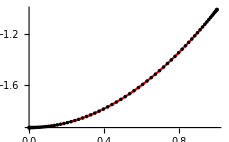
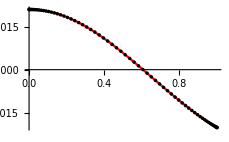
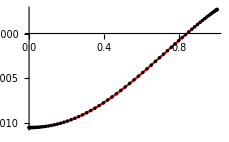
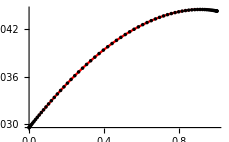
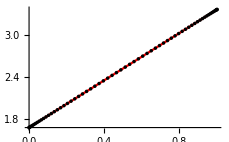
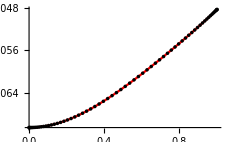

```mathematica
Table[ListPlot[{zgrid,background⟦gSize i+1;;gSize(i+1)⟧}//Transpose,PlotStyle->Black],{i,0,5}];
Plot[backSub⟦#,2⟧[z],{z,0,1},PlotStyle->Red]&/@Range[Length[backSub]];
Show[%⟦#⟧,%%⟦#⟧,ImageSize->230]&/@Range[6]
```

```mathematica
backSub//Precision
backData//Precision
background//Precision
```

60.

57.3307

57.3307

### Use of bgpole

```mathematica
prec1=60;
gSize=1/6 Length[background];
```

```mathematica
coeff[solution_,nz_]:=Block[{Tmatrix,zg},zg=N[Table[Cos[ (r π)/(nz-1)],{r,0,nz-1}],prec1];
Tmatrix=Table[ChebyshevT[k,zg⟦i⟧],{i,1,nz},{k,0,nz-1}];
ParallelTable[LinearSolve[Tmatrix,solution⟦(j-1) nz+1;;j nz⟧],{j,Length[solution]/nz}]]
```

```mathematica
bgpol[solution_, nz_] := Block[{bg},
  bg = coeff[solution, nz].Table[
     ChebyshevT[i, 2 z - 1], {i, 0, nz - 1}];
  Table[{
     functions⟦i⟧->bg⟦i⟧,
     D[functions⟦i⟧, z]->D[bg⟦i⟧, z],
     D[functions⟦i⟧, z,z]->D[bg⟦i⟧, z,z]}, 
{i, 1, Length[functions]}] // Flatten
  ]
```

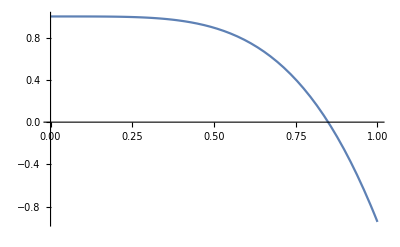
{-Graphics-,-Graphics-}

```mathematica
u[z]/.psub/.bgpol[background,gSize]/.B->bSub;
{Plot[%%,{z,0,1}],Plot[%,{z,0,1}]}
```

### RNS check (OK)

```mathematica
RNS={u->Function[z,1-z^4+1/3 z^4(z^2-1)μ^2],w->Function[z,1],vv->Function[z,1],c->Function[z,0],P->Function[z,0],AV->Function[z,μ z^2-μ],B->0};
```

```mathematica
ftaap=u'[z]/(4π)/.RNS/.z->1
μSub=Solve[mutilde==μ/ftaap,μ]//Flatten//Simplify
```

(-4+(2 μ^2)/3)/(4 π)

{μ→1/10 (3 π-√(600+9 π^2)),μ→1/10 (3 π+√(600+9 π^2))}

```mathematica
psubInv=Solve[{uT[z],wT[z],vT[z],cT[z],PT[z],AVT[z]}=={u[z],w[z],vv[z],c[z],P[z],AV[z]}/.psub,{u[z],w[z],vv[z],c[z],P[z],AV[z]}]/.{uT->u,wT->w,vT->vv,cT->c,PT->P,AVT->AV}//Simplify//Flatten
```

{u[z]→-(6+B^2 z^4 Log[z]-6 u[z])/(6 z^4),w[z]→-1/z^4-1/12 B^2 Log[z]+w[z]/z^4,vv[z]→-1/z^4+1/24 B^2 Log[z]+vv[z]/z^4,c[z]→-c[z]/((-1+z) z^4),P[z]→P[z]/z^2,AV[z]→-AV[z]/(-1+z)}

```mathematica
{u[z],w[z],vv[z],c[z],P[z],AV[z]}/.psub/.psubInv//Simplify
{u[z],w[z],vv[z],c[z],P[z],AV[z]}/.psubInv/.psub//Simplify
```

{u[z],w[z],vv[z],c[z],P[z],AV[z]}

{u[z],w[z],vv[z],c[z],P[z],AV[z]}

```mathematica
μSub⟦1⟧//N
```

μ→-1.68207

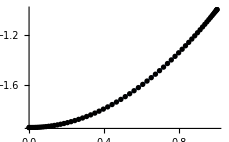
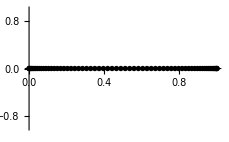
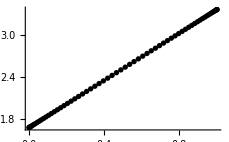
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[{zgrid,background⟦gSize i+1;;gSize(i+1)⟧}//Transpose,PlotStyle->Black],{i,0,5}];
Plot[#,{z,0,1}]&/@({u[z],w[z],vv[z],c[z],AV[z],P[z]}/.psubInv/.RNS/.μSub⟦1⟧//Simplify);
Show[%⟦#⟧,%%⟦#⟧,ImageSize->230]&/@Range[6]
```

```mathematica
Clear[backSub]
```

### Thermodynamics

```mathematica
taap=SetPrecision[1/(4π)Abs[u'[z]/.psub/.backSub/.B->bSub/.z->1],prec1]
entropy=SetPrecision[4π vv[z]^2 w[z]/.psub/.backSub/.B->bSub/.z->1,prec1]
n0=SetPrecision[-D[AV[z]/.psub/.backSub,{z,2}]/.z->0,prec1]
u4=background⟦1⟧;
w4=background⟦68+1⟧;
ϵ0=-3u4
p0=-u4+8w4
w0=ϵ0+p0
```

0.168210461888062175763090739549234723209341751093233143598789

12.5645079065133528533074054714285415393390247577444047977329

3.36615859835511715014603706291118925609913633084809482471445

5.830524758814834099272516265523144249581009312632917404708

1.9451878205702174665942556156845936910010245467104306066355

7.7757125793850515658667718812077379405820338593433480113435

```mathematica
bSub/taap^2
```

2.562311937276675198302371682713841317958367931892172679068

## Green function (ω ≠ 0, k=0)

### Hyperparameter

```mathematica
zBdr=10^-10;
zHor=1-zBdr;

wp=prec1-2; 
pg=21; 
ag=10^2;
```

### Green function

```mathematica
vectorEQN=SetPrecision[vectorAFinal/.psub/.backSub/.{B->bSub,γ->γSub}//Simplify,prec1];

uNot=-SetPrecision[u'[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
vNot=SetPrecision[vv[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
wNot=SetPrecision[w[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
cNot=-SetPrecision[c'[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
avNot=-SetPrecision[AV'[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
pNot=SetPrecision[P[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];

ruleUVWCAVP1=SetPrecision[{u[0]->uNot,v[0]->vNot,w[0]->wNot,c[0]->cNot,av[0]->avNot,p[0]->pNot},prec1];

beingSpecific=SetPrecision[{{c1[0]->z1,cv1[0]-> zV1, c13[0]->z13},{c2[0]->z2,cv2[0]-> zV2, c23[0]->z23},{B->bSub,γ->γSub}}//Flatten,prec1];

positionType=SetPrecision[{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1/.z->zHor,prec1];

velocityType=SetPrecision[D[{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1,z]/.z->zHor,prec1];
```

```mathematica
solSix[omega_?NumericQ,momentum_?NumericQ, hv1Zero_?NumericQ,hv2Zero_?NumericQ,h13Zero_?NumericQ,h23Zero_?NumericQ]:=Block[{ω=omega,k=momentum,zV1=hv1Zero,zV2=hv2Zero, z13=h13Zero,z23=h23Zero},NDSolve[{0== vectorEQN⟦1⟧,0== vectorEQN⟦2⟧, 0==vectorEQN⟦3⟧,0== vectorEQN⟦4⟧,0== vectorEQN⟦5⟧, 0==vectorEQN⟦6⟧,a1[zHor]==positionType⟦1⟧,a2[zHor]== positionType⟦2⟧, hV1[zHor]== positionType⟦3⟧,hV2[zHor]==positionType⟦4⟧,h13[zHor]==positionType⟦5⟧, h23[zHor]==positionType⟦6⟧,a1'[zHor]==velocityType⟦1⟧,a2'[zHor]== velocityType⟦2⟧,hV1'[zHor]==velocityType⟦3⟧,hV2'[zHor]==velocityType⟦4⟧,h13'[zHor]== velocityType⟦5⟧,h23'[zHor]==velocityType⟦6⟧},{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]},{z,zBdr,zHor},MaxSteps->10^6,WorkingPrecision->wp,PrecisionGoal->pg,AccuracyGoal->ag]]

pureGauge1[ω_,k_,B_]={B,0,0,ⅈ ω,0,-ⅈ k}; 
pureGauge2[ω_,k_,B_]={0,B,-ⅈ ω,0,ⅈ k,0};

hIJ[ω_,k_]:=SetPrecision[Transpose[({{pureGauge1[ω,k,bSub]}, {pureGauge2[ω,k,bSub]}, {solSix[ω,k,-1,1,1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,-1,1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,1,-1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,1,1,-1]⟦1,;;,2⟧}})] ,prec1]

hIJ0[ω_,k_]:=SetPrecision[hIJ[ω,k]/.z->zBdr,prec1]
hIJ0I[ω_,k_]:=SetPrecision[Inverse[hIJ0[ω,k]],prec1]
fQ[ω_,k_]:=SetPrecision[hIJ[ω,k].hIJ0I[ω,k],prec1]
fQp[ω_,k_]:=SetPrecision[D[fQ[ω,k],z] ,prec1]

first[ω_,k_]=SetPrecision[Table[firstTotal⟦i,j⟧,{i,6},{j,6}]/.{B->bSub,γ->γSub}//Simplify,prec1];
second[ω_,k_]=SetPrecision[Table[(secondBulk+secondCounter)⟦i,j⟧,{i,6},{j,6}]/.{B->bSub,γ->γSub}//Simplify,prec1];

green[ω_,k_]:=SetPrecision[-2(first[ω,k].fQp[ω,k]+second[ω,k]),prec1]
```

```mathematica
kSub=10^-8;
```

```mathematica
Clear[all,toSave]
```

```mathematica
green[1/100,kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{0.1645818763129063949049718979818665444+0.0001025545639526444132928093246611498 ⅈ,-0.0000593511044674636751910025451733324+0.5167649679839843288711358893123435703 ⅈ,0.410364278851390116631139877501288698+0.000430295507815576460143826619569162 ⅈ,-0.0007435205992357956383428148744577093+1.193218585085609541482683633020907932 ⅈ,-0.0057959963982129796866457701056659372+4.264648150090581670625020811795×10^-7 ⅈ,-0.000010579123641969947270665089632765-0.0181829618215783626273476245145399058 ⅈ},{0.0000593511044674636751910025451733324-0.5167649679839843288711358893123435703 ⅈ,0.1645818763129063949049718979818665444+0.0001025545639526444132928093246611498 ⅈ,0.0007435205992357956383428148744577093-1.193218585085609541482683633020907932 ⅈ,0.410364278851390116631139877501288698+0.000430295507815576460143826619569162 ⅈ,0.000010579123641969947270665089632765+0.0181829618215783626273476245145399058 ⅈ,-0.0057959963982129796866457701056659372+4.264648150090581670625020811795×10^-7 ⅈ},{0.380387240763900316+0.000430295506154792 ⅈ,-0.0007435205959385+1.19321858505513909 ⅈ,2.85937525600931864+0.00539052439726277 ⅈ,-0.00311964242271414+2.75780745351730405 ⅈ,-0.0133905633414787+0.00007670864210171 ⅈ,-3.09189176886×10^-6-0.04202097324129672 ⅈ},{0.0007435205959385-1.19321858505513909 ⅈ,0.380387240763900316+0.000430295506154792 ⅈ,0.00311964242271414-2.75780745351730405 ⅈ,2.85937525600931864+0.00539052439726277 ⅈ,3.09189176886×10^-6+0.04202097324129672 ⅈ,-0.0133905633414787+0.00007670864210171 ⅈ},{-0.00579599647450199+4.2646608899×10^-7 ⅈ,-0.00001057912333926-0.01818296205562051 ⅈ,-0.0133905650348527+0.00007670864049994 ⅈ,-3.0918783263×10^-6-0.0420209738002123 ⅈ,-1.98018357491839396+0.00999629031753422 ⅈ,8.1887054267×10^-7+0.000639927132956 ⅈ},{0.00001057912333926+0.01818296205562051 ⅈ,-0.00579599647450199+4.2646608899×10^-7 ⅈ,3.0918783263×10^-6+0.0420209738002123 ⅈ,-0.0133905650348527+0.00007670864049994 ⅈ,-8.1887054267×10^-7-0.000639927132956 ⅈ,-1.98018357491839396+0.00999629031753422 ⅈ}}

```mathematica
green[4,kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{-20.608288376471690088391894129374079864+25.844109430171766320144347523012354585 ⅈ,0.042050903050398368153603008071904725-0.028539377269698499606255914138594325 ⅈ,-3.33669882182241261055727676835903698305-0.00076217262635376372612990546751623195 ⅈ,-0.46842448342571507512452278671697827786-0.37352522682524066113983116161385081512 ⅈ,0.13528362387840185701698094261673519-0.0034261173213383403784851835262364451 ⅈ,-0.001540724228762595144952026805224694-0.0006765113150912322075782470355680145 ⅈ},{-0.042050903050398368153603008071904725+0.028539377269698499606255914138594325 ⅈ,-20.608288376471690088391894129374079864+25.844109430171766320144347523012354585 ⅈ,0.46842448342571507512452278671697827786+0.37352522682524066113983116161385081512 ⅈ,-3.33669882182241261055727676835903698305-0.00076217262635376372612990546751623195 ⅈ,0.001540724228762595144952026805224694+0.0006765113150912322075782470355680145 ⅈ,0.13528362387840185701698094261673519-0.0034261173213383403784851835262364451 ⅈ},{-3.3666758599699866-0.0007621741029321 ⅈ,-0.4684244834225112-0.373525226781588 ⅈ,-5.798229498549418111+0.008490193762103456 ⅈ,0.00001381440577089-0.061020999955825968 ⅈ,0.1184234303187147+0.0000281766136009 ⅈ,0.00006209858110532+0.0024520157093534 ⅈ},{0.4684244834225112+0.373525226781588 ⅈ,-3.3666758599699866-0.0007621741029321 ⅈ,-0.00001381440577089+0.061020999955825968 ⅈ,-5.798229498549418111+0.008490193762103456 ⅈ,-0.00006209858110532-0.0024520157093534 ⅈ,0.1184234303187147+0.0000281766136009 ⅈ},{0.1352836453841898-0.0034261413798143 ⅈ,-0.0015578648238544-0.0006624833311127 ⅈ,0.11842368455598602+0.000028487273464219 ⅈ,0.000062098812648566+0.002452016072649556 ⅈ,-87.47720638979659245+100.3894127433873257 ⅈ,0.00005577292856249+0.0000244461997448 ⅈ},{0.0015578648238544+0.0006624833311127 ⅈ,0.1352836453841898-0.0034261413798143 ⅈ,-0.000062098812648566-0.002452016072649556 ⅈ,0.11842368455598602+0.000028487273464219 ⅈ,-0.00005577292856249-0.0000244461997448 ⅈ,-87.47720638979659245+100.3894127433873257 ⅈ}}

```mathematica
SetPrecision[green[4,kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1]
```

{{-20.608288376471690088391894129374079863690610067532007253089+25.8441094301717663201443475230123545849071837550285686862572 ⅈ,0.0420509030503983681536030080719047246211750182480229746856305-0.028539377269698499606255914138594324785935686035071815182572 ⅈ,-3.3366988218224126105572767683590369830450804100314656591687-0.00076217262635376372612990546751623194934990983964986220533 ⅈ,-0.468424483425715075124522786716978277864911195996944745429028-0.37352522682524066113983116161385081511830574911161286633933 ⅈ,0.135283623878401857016980942616735190423402775831099419466619-0.00342611732133834037848518352623644505355767946890827299258 ⅈ,-0.00154072422876259514495202680522469410156259672012468523568907-0.0006765113150912322075782470355680144950230425137989072912504 ⅈ},{-0.0420509030503983681536030080719047246211750182480229746856305+0.028539377269698499606255914138594324785935686036664907093704 ⅈ,-20.608288376471690088391894129374079863690610067530414161178+25.8441094301717663201443475230123545849071837550285686862572 ⅈ,0.468424483425715075124522786716978277864911195996945517633177+0.37352522682524066113983116161385081511830574911161242459087 ⅈ,-3.33669882182241261055727676835903698304508041003146563227158-0.00076217262635376372612990546751623194934990983964985181997 ⅈ,0.00154072422876259514495202680522469410156259672012468523568907+0.0006765113150912322075782470355680144950230425137989072912504 ⅈ,0.135283623878401857016980942616735190423402775831099419466619-0.00342611732133834037848518352623644505355767946890827299258 ⅈ},{-3.36667585996998658495640563807076855525270954885823209519662-0.00076217410293213124846163209393247901295283538561143629959 ⅈ,-0.468424483422511165248583449704055013425517884072685385625823-0.37352522678158795729532130848689870368449046948357315131871 ⅈ,-5.79822949854941811132508588313737194759726437315316339961367+0.00849019376210345640413278688154927044093284340292627344083 ⅈ,0.000013814405770891331641665779023157393338234425059626435997-0.0610209999558259675789512300658492503714474050663064688547521 ⅈ,0.118423430318714748123555793325174291818330558066973423368666+0.000028176613600884743301670524710845982543044002877164137677 ⅈ,0.00006209858110531948043353009996470442115457257871695631785015+0.00245201570935344885018233440604151148405591395160990376959553 ⅈ},{0.468424483422511165248583449704055013425517884072685385625823+0.37352522678158795729532130848689870368449046948357315131871 ⅈ,-3.36667585996998658495640563807076855525270954885823209519662-0.00076217410293213124846163209393247901295283538561143629959 ⅈ,-0.000013814405770891331641665779023157393338234425059626435997+0.0610209999558259675789512300658492503714474050663064688547521 ⅈ,-5.79822949854941811132508588313737194759726437315316339961367+0.00849019376210345640413278688154927044093284340292627344083 ⅈ,-0.00006209858110531948043353009996470442115457257871695631785015-0.00245201570935344885018233440604151148405591395160990376959553 ⅈ,0.118423430318714748123555793325174291812453086312861985828822+0.000028176613600884743301670524710845982543044002877164137677 ⅈ},{0.135283645384189833556245571202064555194474896025073365260655-0.003426141379814255746517916849088067577798044256257062460284 ⅈ,-0.00155786482385435795681196225216510413976659598795863094741113-0.00066248333111272911812072819926288112422928030001801602555488 ⅈ,0.118423684555986024301812697704774982841069043653025418123458+0.000028487273464218706281538579730663229282589391929416607078 ⅈ,0.00006209881264856570681186756999165003793909816511529980966045+0.0024520160726495562325690432014804686955410219157473736513098 ⅈ,-87.477206389796592453690188707953084366323067778047445076215+100.389412743387325728702142466190867775711565846259990266084 ⅈ,0.000055772928562492131296796900758660510485634470493280194040818+0.000024446199744836890444582095132792195001670887840438096777451 ⅈ},{0.00155786482385435795681196273009267748295333919564611807867149+0.00066248333111272911812072851788126334910212793573538241983267 ⅈ,0.135283645384189833556245570724136981857165624571497315669239-0.003426141379814255746517916849088067577798044256257062460284 ⅈ,-0.00006209881264856570681186756998658195282024541363906800051704-0.00245201607264955623256904319728627926717255444022731074695009 ⅈ,0.118423684555986024301812697702455862696405910984590358632465+0.000028487273464218706281538579098914426236479656028821546317 ⅈ,-0.000055772928562492131296796900758660510485634470493280194040818-0.000024446199744836890444582413751174425751990277669242030898921 ⅈ,-87.477206389796592453690188708112393557435504201865303759412+100.389412743387325728702142466190867775711565846259990266084 ⅈ}}

```mathematica
green[7,kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{-89.6292473890355863169295876540403258813+76.9507256828891417391265711435058568578 ⅈ,-0.001739438099484335964412315091096355-0.015729704366912630753598974389079586 ⅈ,-3.33634446040595078900527600227115566549+0.00001801560906828877355212865633518517 ⅈ,-0.796989658858229525372599072129041950366-0.928302919386533215341667700446221313842 ⅈ,0.095001718330915489694236994826758168+0.000126540705744500775024181049511306 ⅈ,0.000185609847848290300087595763334414-0.0000652499414278798205625570496842934 ⅈ},{0.001739438099484335964412315091096355+0.015729704366912630753598974389079586 ⅈ,-89.6292473890355863169295876540403258813+76.9507256828891417391265711435058568578 ⅈ,0.796989658858229525372599072129041950366+0.928302919386533215341667700446221313842 ⅈ,-3.33634446040595078900527600227115566549+0.00001801560906828877355212865633518517 ⅈ,-0.000185609847848290300087595763334414+0.0000652499414278798205625570496842934 ⅈ,0.095001718330915489694236994826758168+0.000126540705744500775024181049511306 ⅈ},{-3.3663214933878962+0.0000180175119177 ⅈ,-0.7969896588945687-0.9283029193754589 ⅈ,-5.801073919764648248+0.008254535752835783 ⅈ,-1.86609946734×10^-7-0.034865472608683287 ⅈ,0.1184336576589385-5.753289526×10^-7 ⅈ,-1.3105749021×10^-6+0.00098394657489372 ⅈ},{0.7969896588945687+0.9283029193754589 ⅈ,-3.3663214933878962+0.0000180175119177 ⅈ,1.86609946734×10^-7+0.034865472608683287 ⅈ,-5.801073919764648248+0.008254535752835783 ⅈ,1.3105749021×10^-6-0.00098394657489372 ⅈ,0.1184336576589385-5.753289526×10^-7 ⅈ},{0.0950018054852588+0.0001265303591551 ⅈ,0.0001526280805811-0.00005221160791934 ⅈ,0.118433792778851826-2.33803698403×10^-7 ⅈ,-1.310493038673×10^-6+0.0009839472710865015 ⅈ,-1102.5640212790008459+942.89099533097106676 ⅈ,-0.0000231967247002-7.57526833552×10^-6 ⅈ},{-0.0001526280805811+0.00005221160791934 ⅈ,0.0950018054852588+0.0001265303591551 ⅈ,1.310493038673×10^-6-0.0009839472710865015 ⅈ,0.118433792778851826-2.33803698403×10^-7 ⅈ,0.0000231967247002+7.57526833552×10^-6 ⅈ,-1102.5640212790008459+942.89099533097106676 ⅈ}}

### σ_DC Koreans

```mathematica
σDC=(2 π eE^2 T^2)/(-1 + 3 √(1 + 2/(3 π^2)μT^2))/.{T->taap,μT->μSub}
```

0.024173174169300133174487362211026227633948204755891539729301 eE^2

```mathematica
smallω=green[1/100,0]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{-1.456132225599464237894776471554773632+0.0007396934984887158852144472630340796 ⅈ,-6.403301500073505827910870907909×10^-7-0.0006302016927664994220601211532529543 ⅈ,-3.36414453731577305781623777199610086382+6.403301500073505827910870907909×10^-10 ⅈ,-7.396934984887158852144472630340796×10^-7-0.001456132225599464237894776471554773632 ⅈ,7.0702563442662762152519571905706×10^-6-8.5203581072724214626172162941×10^-9 ⅈ,5.2424304087441963835220608×10^-12+3.06024424032927077934093279×10^-9 ⅈ},{6.403301500073505827910870907909×10^-7+0.0006302016927664994220601211532529543 ⅈ,-1.456132225599464237894776471554773632+0.0007396934984887158852144472630340796 ⅈ,7.396934984887158852144472630340796×10^-7+0.001456132225599464237894776471554773632 ⅈ,-3.36414453731577305781623777199610086382+6.403301500073505827910870907909×10^-10 ⅈ,-5.2424304087441963835220608×10^-12-3.06024424032927077934093279×10^-9 ⅈ,7.0702563442662762152519571905706×10^-6-8.5203581072724214626172162941×10^-9 ⅈ},{-3.36414568328583708+6.4904328×10^-10 ⅈ,-7.3969350251×10^-7-0.0014561322255601 ⅈ,-5.82936944004741088+7.3969350251×10^-10 ⅈ,-6.4904328×10^-13-0.00336414568328583708 ⅈ,0.0000163353667349-5.35×10^-15 ⅈ,8.5203×10^-12+7.07025634×10^-9 ⅈ},{7.3969350251×10^-7+0.0014561322255601 ⅈ,-3.36414568328583708+6.4904328×10^-10 ⅈ,6.4904328×10^-13+0.00336414568328583708 ⅈ,-5.82936944004741088+7.3969350251×10^-10 ⅈ,-8.5203×10^-12-7.07025634×10^-9 ⅈ,0.0000163353667349-5.35×10^-15 ⅈ},{7.07026683616×10^-6-8.52035154×10^-9 ⅈ,5.24244×10^-12+3.0602488×10^-9 ⅈ,0.0000163353667359541-5.24244×10^-15 ⅈ,8.52035154×10^-12+7.07026683616×10^-9 ⅈ,-1.9430904010524402+0.0100007790226766 ⅈ,-4.×10^-17-1.49×10^-14 ⅈ},{-5.24244×10^-12-3.0602488×10^-9 ⅈ,7.07026683616×10^-6-8.52035154×10^-9 ⅈ,-8.52035154×10^-12-7.07026683616×10^-9 ⅈ,0.0000163353667359541-5.24244×10^-15 ⅈ,4.×10^-17+1.49×10^-14 ⅈ,-1.9430904010524402+0.0100007790226766 ⅈ}}

```mathematica
bSub^2/w0^2 smallω⟦3,3⟧/ω/.{ω->1/100};
%^-1/taap
```

-6.161109442867417426×10^9-0.78178826544 ⅈ

```mathematica
Solve[σDC==0.78,eE]//Flatten
```

{eE→-5.68042,eE→5.68042}

```mathematica
smalllω=green[10^-5,0]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{-1.791760620275999615369190669498221778+1.329673914105563978787254361293×10^-6 ⅈ,-9.694262788208410895287112608779×10^-7-0.7755226607425884403988134765211292434 ⅈ,-4.139666567856668731715629188396076854+9.694262788208410895287112608779×10^-7 ⅈ,-1.329673914105563978787254361293×10^-6-1.791760620275999615369190669498221778 ⅈ,8.7002970702787220621273374024838×10^-6-1.2520994915174646387587887×10^-11 ⅈ,7.3321093502260154543874594×10^-12+3.7657248727071908947946614348454×10^-6 ⅈ},{9.694262788208410895287112608779×10^-7+0.7755226607425884403988134765211292434 ⅈ,-1.791760620275999615369190669498221778+1.329673914105563978787254361293×10^-6 ⅈ,1.329673914105563978787254361293×10^-6+1.791760620275999615369190669498221778 ⅈ,-4.139666567856668731715629188396076854+9.694262788208410895287112608779×10^-7 ⅈ,-7.3321093502260154543874594×10^-12-3.7657248727071908947946614348454×10^-6 ⅈ,8.7002970702787220621273374024838×10^-6-1.2520994915174646387587887×10^-11 ⅈ},{-4.13966771380523296+9.6942628968×10^-7 ⅈ,-1.3296739191×10^-6-1.7917606202272721 ⅈ,-7.62112860414245737+1.3296739191×10^-6 ⅈ,-9.6942628968×10^-7-4.13966771380523296 ⅈ,0.00002010108854726-7.33211×10^-12 ⅈ,1.252094×10^-11+8.70029707002×10^-6 ⅈ},{1.3296739191×10^-6+1.7917606202272721 ⅈ,-4.13966771380523296+9.6942628968×10^-7 ⅈ,9.6942628968×10^-7+4.13966771380523296 ⅈ,-7.62112860414245737+1.3296739191×10^-6 ⅈ,-1.252094×10^-11-8.70029707002×10^-6 ⅈ,0.00002010108854726-7.33211×10^-12 ⅈ},{8.70030998198×10^-6-1.2521×10^-11 ⅈ,7.33214×10^-12+3.7657304613×10^-6 ⅈ,0.000020101094137-7.33214×10^-12 ⅈ,1.2521×10^-11+8.70030998198×10^-6 ⅈ,-1.9431226622650157+0.0000100000000008 ⅈ,-5.×10^-17-1.82854×10^-11 ⅈ},{-7.33214×10^-12-3.7657304613×10^-6 ⅈ,8.70030998198×10^-6-1.2521×10^-11 ⅈ,-1.2521×10^-11-8.70030998198×10^-6 ⅈ,0.000020101094137-7.33214×10^-12 ⅈ,5.×10^-17+1.82854×10^-11 ⅈ,-1.9431226622650157+0.0000100000000008 ⅈ}}

```mathematica
bSub^2/w0^2 smalllω⟦3,3⟧/ω/.{ω->10^-5};
%^-1/taap
```

-4.7126068812847465×10^6-0.82221817611 ⅈ

```mathematica
Solve[σDC==0.822,eE]//Flatten
```

{eE→-5.83135,eE→5.83135}

```mathematica
small4ω=green[10^-7,0]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{0.000777664174529643260109690641333283882+3.95416937606504797290794854×10^-12 ⅈ,-1.8261613535524853888504438×10^-13+0.03365941761529691797277715852398584798 ⅈ,0.001797854415611505960900140523637187+1.8261613535524853888504438×10^-11 ⅈ,-3.95416937606504797290794854×10^-10+0.0777664174529643260109690641333283882 ⅈ,-3.7761234556049889516984474318×10^-9+6.5882726612854053498×10^-18 ⅈ,-1.13835110887411439429×10^-15-1.63440879969733506272405808171×10^-7 ⅈ},{1.8261613535524853888504438×10^-13-0.03365941761529691797277715852398584798 ⅈ,0.000777664174529643260109690641333283882+3.95416937606504797290794854×10^-12 ⅈ,3.95416937606504797290794854×10^-10-0.0777664174529643260109690641333283882 ⅈ,0.001797854415611505960900140523637187+1.8261613535524853888504438×10^-11 ⅈ,1.13835110887411439429×10^-15+1.63440879969733506272405808171×10^-7 ⅈ,-3.7761234556049889516984474318×10^-9+6.5882726612854053498×10^-18 ⅈ},{0.001796708354418701+1.8261607×10^-11 ⅈ,-3.954169354×10^-10+0.077766417450849441 ⅈ,1.9472737611697588+3.954169354×10^-8 ⅈ,-1.8261607×10^-9+0.1796708354418701 ⅈ,-8.72432188×10^-9+1.1384×10^-13 ⅈ,-7.1×10^-16-3.7761234748×10^-7 ⅈ},{3.954169354×10^-10-0.077766417450849441 ⅈ,0.001796708354418701+1.8261607×10^-11 ⅈ,1.8261607×10^-9-0.1796708354418701 ⅈ,1.9472737611697588+3.954169354×10^-8 ⅈ,7.1×10^-16+3.7761234748×10^-7 ⅈ,-8.72432188×10^-9+1.1384×10^-13 ⅈ},{-3.776129079×10^-9+7.1×10^-18 ⅈ,-1.138×10^-15-1.63441122525×10^-7 ⅈ,-8.7485768×10^-9+1.138×10^-13 ⅈ,-7.1×10^-16-3.776129079×10^-7 ⅈ,-1.943122662255013+1.×10^-7 ⅈ,0.+7.9363×10^-13 ⅈ},{1.138×10^-15+1.63441122525×10^-7 ⅈ,-3.776129079×10^-9+7.1×10^-18 ⅈ,7.1×10^-16+3.776129079×10^-7 ⅈ,-8.7485768×10^-9+1.138×10^-13 ⅈ,0.-7.9363×10^-13 ⅈ,-1.943122662255013+1.×10^-7 ⅈ}}

```mathematica
bSub^2/w0^2 small4ω⟦3,3⟧/ω/.{ω->10^-7};
%^-1/taap
```

184439.31109852724-0.003745258043 ⅈ

### ω grid

```mathematica
prec1=60;
ωgSize=50;
ωAxis=SetPrecision[Table[L+ (1-Cos[(n π)/(2ωgSize-1)])(U-L),{n,0,2ωgSize-1}]⟦;;ωgSize⟧/.{L->10^-2,U->16π taap},prec1];
```

```mathematica
{ωAxis/(4π taap),ωAxis}//Transpose//ListPlot
```

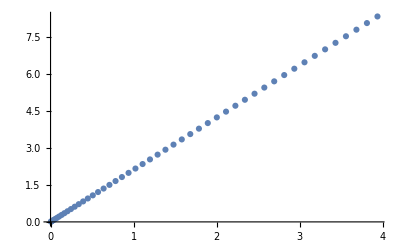

### Computation

```mathematica
all=SetPrecision[green[#,kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1]&/@ωAxis
```

{{{0.164581876312906394904971897981866544358793419151710287850939+0.0001025545639526444132928093246611497519244730845841014542 ⅈ,4,-97-97 ⅈ},4,{1}},48,{1}}
 |  |  |  |

```mathematica
toSave={{2/(√3),mutilde,bSub,taap,entropy,n0,p0,kSub},all};
```

To save the normal correlator

```mathematica
Beep[]
```

```mathematica
"corChiralγSUSYμT"<>ToString[100mutilde]<>"d100B"<>ToString[10^6 bSub]<>"d10p6"
```

corChiralγSUSYμT1000d100B72500d10p6

```mathematica
SetDirectory[NotebookDirectory[]<>"Chiral_conductivity"];
Save["corChiralγSUSYμT"<>ToString[100mutilde]<>"d100B"<>ToString[10^6 bSub]<>"d10p6",toSave]
```

Another

```mathematica
allΔ=ParallelMap[SetPrecision[green[#,kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1]&,ωAxis]

toSaveΔ={{2/(√3),mutilde,bSub,taap,entropy,n0,p0,kSub},allΔ};
```

To save the μ + Δμ correlator

```mathematica
SetDirectory[NotebookDirectory[]<>"Chiral_conductivity"];
Save["corChiralγSUSYμT"<>ToString[100Round[mutilde]]<>"d100ΔμB"<>ToString[10^6 bSub]<>"d10p6",toSaveΔ]
```

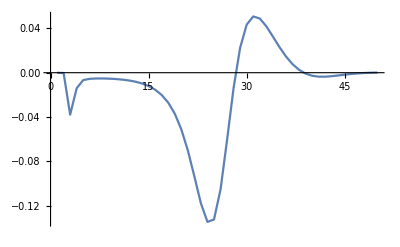
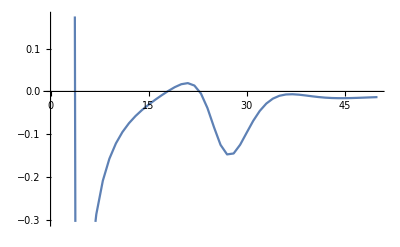

```mathematica
all⟦All,1,2⟧;
{ListPlot[Re[%],Joined->True],ListPlot[Im[%],Joined->True]}
```

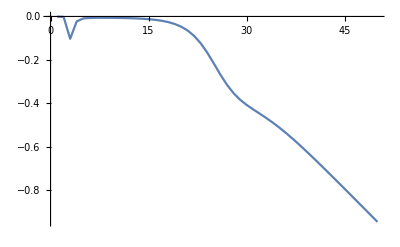
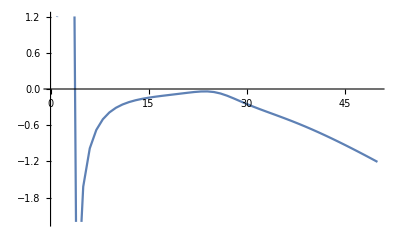

```mathematica
all⟦All,1,4⟧;
{ListPlot[Re[%],Joined->True],ListPlot[Im[%],Joined->True]}
```

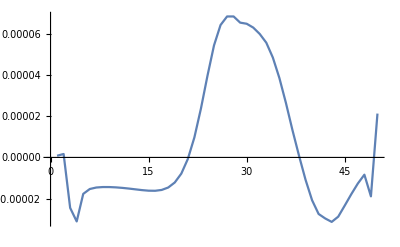
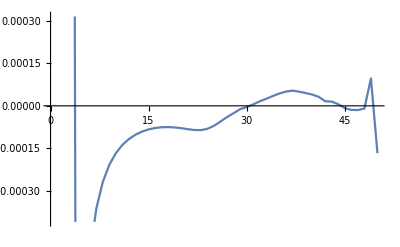

```mathematica
all⟦All,5,6⟧;
{ListPlot[Re[%],Joined->True],ListPlot[Im[%],Joined->True]}
```